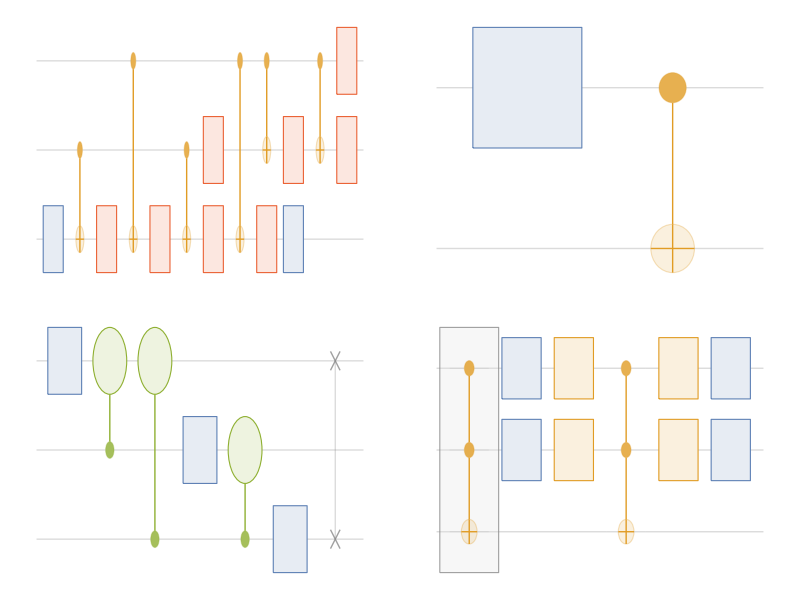
Reinstall Paclet
QuanumState
01ψ_(x_+)ψ_(x_-)
(0+1)/(√2)1/2 (00+11)
QuantumOperator
QFTQFT^†XYZ
QuantumMeasurementOperator
IXYZ
QuantumCircuitOperator
-Graphics-
Functions
QuantumTensorProduct
QuantumEntanglementMonotone
QuantumEntangledQ
QuantumDistance

```mathematica
palette = PaletteNotebook[Column[{

Button["Reinstall Paclet",
	PacletInstall[CloudObject["https://wolfr.am/DevWQCF"], ForceVersionInstall -> True];
	<< Wolfram`QuantumFramework`
],

"QuanumState",
Column[{Row @ {
	PasteButton[QuantumState["0"]["Formula"], Unevaluated @ QuantumState["0"]],
	PasteButton[QuantumState["1"]["Formula"], Unevaluated @ QuantumState["1"]],
	PasteButton[QuantumState["Plus", "X"]["Formula"], Unevaluated @ QuantumState["+"]],
	PasteButton[QuantumState["Minus", "X"]["Formula"], Unevaluated @ QuantumState["-"]]
	},
	Row[{
		PasteButton[Simplify[QuantumState["UniformSuperposition"]["Formula"]], Unevaluated @ QuantumState["UniformSuperposition"]],
		PasteButton[Simplify[QuantumState["UniformMixture"]["Formula"]], Unevaluated @ QuantumState["UniformMixture"]]
	}]
}],

"QuantumOperator",
Row @ {
	PasteButton[QuantumOperator["Fourier"]["Label"], Unevaluated @ QuantumOperator["Fourier"]],
	PasteButton[QuantumOperator["InverseFourier"]["Label"], Unevaluated @ QuantumOperator["InverseFourier"]],
	PasteButton[QuantumOperator["X"]["Label"], Unevaluated @ QuantumOperator["X"]],
	PasteButton[QuantumOperator["Y"]["Label"], Unevaluated @ QuantumOperator["Y"]],
	PasteButton[QuantumOperator["Z"]["Label"], Unevaluated @ QuantumOperator["Z"]]
},

"QuantumMeasurementOperator",
Row @ {
	PasteButton["I", Unevaluated @ QuantumMeasurementOperator[]],
	PasteButton[QuantumMeasurementOperator["X"]["Label"], Unevaluated @ QuantumMeasurementOperator["X"]],
	PasteButton[QuantumMeasurementOperator["Y"]["Label"], Unevaluated @ QuantumMeasurementOperator["Y"]],
	PasteButton[QuantumMeasurementOperator["Z"]["Label"], Unevaluated @ QuantumMeasurementOperator["Z"]]
},

"QuantumCircuitOperator",
Grid @ {
	{
		PasteButton[QuantumCircuitOperator["Toffoli"]["Icon"], Unevaluated @ QuantumCircuitOperator["Toffoli"]],
		PasteButton[QuantumCircuitOperator["Bell"]["Icon"], Unevaluated @ QuantumCircuitOperator["Bell"]]
	},
	{
		PasteButton[QuantumCircuitOperator[{"Fourier", 3}]["Icon"], Unevaluated @ QuantumCircuitOperator[{"Fourier", 3}]],
		PasteButton[QuantumCircuitOperator[{"Grover", a && b}]["Icon"], Unevaluated @ QuantumCircuitOperator[{"Grover", a && b}]]
	}
},

"Functions",
Column[{
	PasteButton[QuantumTensorProduct, Unevaluated @ QuantumTensorProduct[Placeholder[], Placeholder[]]],
	PasteButton[QuantumEntanglementMonotone, Unevaluated @ QuantumEntanglementMonotone[Placeholder[]]],
	PasteButton[QuantumEntangledQ, Unevaluated @ QuantumEntangledQ[Placeholder[]]],
	PasteButton[QuantumDistance, Unevaluated @ QuantumDistance[Placeholder[], Placeholder[]]]
}]
}]]
```

#### Save

```mathematica
nb=CreateWindow[palette,Visible->False];
Export[ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","QuantumFramework","FrontEnd","Palettes","QuantumFrameworkPalette.nb"}],nb];
NotebookClose[nb]
```